# Fat tail - finite moments case

## The body the shoulders and the tails

Let X be a PDF with p(x) from a general class of unimodal, one parameter continuous pdfs p_σ  with support D ⊆ R and scale parameter σ
The density p(x) satisfies:

p(x) <= p(x+ϵ)  for x>x_0   and  p(x-ϵ) <=  p(x)  for x<= x_0  with  x_0 = argmax p(x).

The class of quasi concave functions is defined as follows. For all x and y in the domain and ω ∈ [0,1] functions is defined as satisfying:

p(ω x + (1-ω ) y ) >= min(p(x),p(y))

Let us define the two tail distribution p^δ(x) = p_(σ+δ)(x)+p_(σ-δ)(x)/2 for a small δ, i.e. introducing some addition stochasticity on the scale parameter. 

Such unimodal distributions have three areas
1.- High peak: x ∈ (a_2, a_3)  p^δ(x) ≥ p(x)  
2.- Sounders: x ∈ (a_1, a_2) ∪ (a_3, a_4)   p(x)≥ p^δ(x)  
3.- Tails: x ∈ (-∞, a_1) ∪ (a_4, ∞)   p^δ(x) ≥ p(x)  

that satisfy the differential equation, i.e inflexion points !:  

(∂^2 p(x))/(∂ σ^2) = 0

## Gaussian case

```mathematica
p[x_, μ_,σ_ ]:=PDF[NormalDistribution[μ,σ],x]
pdelta1[x_,μ_,σ_,delta_]:=(p[x, μ,σ+delta]+p[x, μ,σ-delta ])/2
pdelta2[x_,μ_,σ_,delta_]:=(p[x, μ,σ √(1+delta)]+p[x, μ,σ √(1-delta) ])/2
```

```mathematica
Solutions= Solve[D[D[p[x, μ,σ ],σ],σ]==0, x]
```

{{x→1/2 (2 μ-√2 √(5 σ^2-√17 σ^2))},{x→1/2 (2 μ+√2 √(5 σ^2-√17 σ^2))},{x→1/2 (2 μ-√2 √(5 σ^2+√17 σ^2))},{x→1/2 (2 μ+√2 √(5 σ^2+√17 σ^2))}}

```mathematica
Limit[(p[x, μ,σ ]/pdelta1[x,μ,σ,delt]),delt->0]
Limit[(p[x, μ,σ ]/pdelta2[x,μ,σ,delt]),delt->0]
```

1

1

```mathematica
Solutions/.{σ->1,μ->0,delt->0.9}//N
```

{{x→-0.662153},{x→0.662153},{x→-2.13578},{x→2.13578}}

The following graph compares and shows that, the the variance is standard deviation is varied, some parts of 
of the gaussian get fatter, while other thinner.

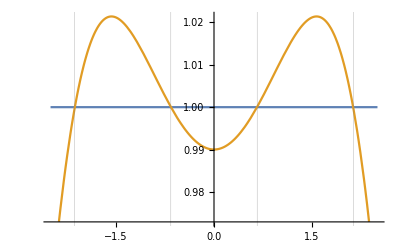

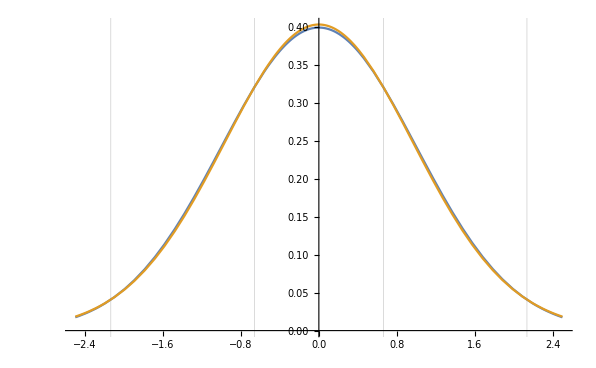

```mathematica
toPlot= {1,p[x, μ,σ ]/pdelta1[x,μ,σ,delt] }/.{σ->1,μ->0,delt->0.1};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]
toPlot= {p[x, μ,σ ],pdelta1[x,μ,σ,delt] }/.{σ->1,μ->0,delt->0.1};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]
```

This is not exactly the case for the variance preserving case which we ignore hereafter

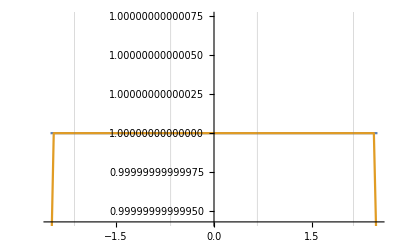

```mathematica
toPlot= {1,p[x, μ,σ ]/pdelta2[x,μ,σ,delt] }/.{σ->1,μ->0,delt->0.000001};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]
```

However as delta grows, the points at which the two PDF interset, the original one and the delta perturbed one, change:

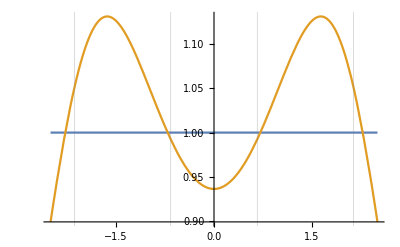

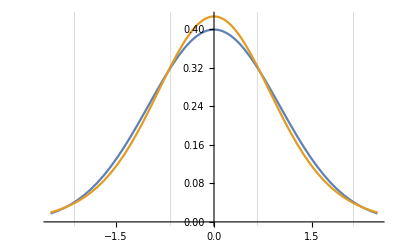

```mathematica
toPlot= {1,p[x, μ,σ ]/pdelta2[x,μ,σ,delt]}/.{σ->1,μ->0,delt->0.4};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]

toPlot= {p[x, μ,σ ],pdelta2[x,μ,σ,delt] }/.{σ->1,μ->0,delt->0.4};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]
```

Hence we conclude the definitio is only effective assymptotically as delta tends to zero.

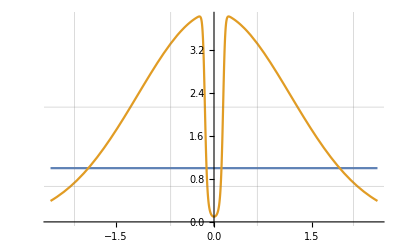

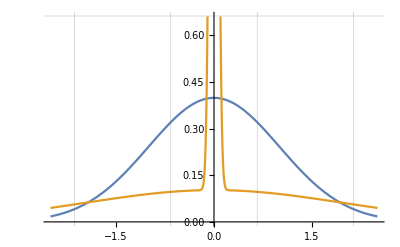

```mathematica
toPlot= {1,p[x, μ,σ ]/pdelta1[x,μ,σ,delt] }/.{σ->1,μ->0,delt->0.95};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]
toPlot= {p[x, μ,σ ],pdelta1[x,μ,σ,delt] }/.{σ->1,μ->0,delt->0.95};
Plot[toPlot,{x,-2.5,2.5},GridLines->{{-0.662153,0.662153, -2.13577, 2.13577} }]
```

```mathematica
p[1/2 (2 μ-√2 √(5 σ^2-√17 σ^2))]
```

## Student T Distribuion with scale s and tail exponent α

```mathematica
st[x_, α_, s_]:=((α/(α+ x^2/s^2))^((α+1)/2))/(Sqrt[α]s Beta[α/2,1/2])
```

Let us re-express this expression in terns of its variance:

```mathematica
Integrate[st[x,α,s]1,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]
```

1

```mathematica
Integrate[st[x,α,s]x,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]
```

0

```mathematica
Integrate[st[x,α,s]x^2 ,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]
```

(s^2 α)/(-2+α)

```mathematica
VarianceDefinition = Solve[ Integrate[st[x,α,s]x^2 ,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]==σ^2,σ]
AlphaDefinition = Solve[ Integrate[st[x,α,s]x^2 ,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]==σ^2, α]
```

{{σ→-(s √α)/(√(-2+α))},{σ→(s √α)/(√(-2+α))}}

{{α→(2 σ^2)/(-s^2+σ^2)}}

```mathematica
zeros = {x->-(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2),x->-(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),x->(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),x->(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2)} ;
zerovalues = {-(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2),-(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2)}/.AlphaDefinition [[1]]
```

{-(s √((1+(10 σ^2)/(-s^2+σ^2)+√((1+(2 σ^2)/(-s^2+σ^2)) (1+(34 σ^2)/(-s^2+σ^2))))/(-1+(2 σ^2)/(-s^2+σ^2))))/(√2),-(s √((1+(10 σ^2)/(-s^2+σ^2)-√((1+(2 σ^2)/(-s^2+σ^2)) (1+(34 σ^2)/(-s^2+σ^2))))/(-1+(2 σ^2)/(-s^2+σ^2))))/(√2),(s √((1+(10 σ^2)/(-s^2+σ^2)-√((1+(2 σ^2)/(-s^2+σ^2)) (1+(34 σ^2)/(-s^2+σ^2))))/(-1+(2 σ^2)/(-s^2+σ^2))))/(√2),(s √((1+(10 σ^2)/(-s^2+σ^2)+√((1+(2 σ^2)/(-s^2+σ^2)) (1+(34 σ^2)/(-s^2+σ^2))))/(-1+(2 σ^2)/(-s^2+σ^2))))/(√2)}

```mathematica
SecondDerivarive = (D[D[(st[x ,α ,s]/.AlphaDefinition), σ], σ]);
SecondDerivarive=SecondDerivarive/.VarianceDefinition[[2]];
```

```mathematica
For[i=1,i<=4,i++,
Print[SecondDerivarive/. zeros[[i]]/.{α->4, s->10} //N] ]
```

{-0.0000539816}

{0.0000956958}

{0.0000956958}

{-0.0000539816}

```mathematica
For[i=1,i<=4,i++,
Print[SecondDerivarive/. zeros[[i]]/.{α->3, s->2.5} //N] ]
```

{-0.00100278}

{0.00249516}

{0.00249516}

{-0.00100278}

```mathematica
prev= (st[x, α,s]/.AlphaDefinition[[1]] ) ;
pst[x_,s_,σ_ ]=prev
```

(2^(-1/2+1/2 (1+(2 σ^2)/(-s^2+σ^2))) (σ^2/((-s^2+σ^2) (x^2/s^2+(2 σ^2)/(-s^2+σ^2))))^(1/2 (1+(2 σ^2)/(-s^2+σ^2))))/(s √(σ^2/(-s^2+σ^2)) Beta[σ^2/(-s^2+σ^2),1/2])

```mathematica
pstdelta2[x_,s_ ,σ_,delt_]=(pst[x, s,σ √(1+delt)]+pst[x, s,σ √(1-delt) ])/2 ;
pstdelta1[x_,s_ ,σ_,delt_]=(pst[x, s,σ+delt]+pst[x, s,σ-delt ])/2 ;
```

```mathematica
pstdelta1[x,s,σ,d]
```

1/2 ((2^(-1/2+1/2 (1+(2 (-d+σ)^2)/(-s^2+(-d+σ)^2))) ((-d+σ)^2/((-s^2+(-d+σ)^2) (x^2/s^2+(2 (-d+σ)^2)/(-s^2+(-d+σ)^2))))^(1/2 (1+(2 (-d+σ)^2)/(-s^2+(-d+σ)^2))))/(s √((-d+σ)^2/(-s^2+(-d+σ)^2)) Beta[(-d+σ)^2/(-s^2+(-d+σ)^2),1/2])+(2^(-1/2+1/2 (1+(2 (d+σ)^2)/(-s^2+(d+σ)^2))) ((d+σ)^2/((-s^2+(d+σ)^2) (x^2/s^2+(2 (d+σ)^2)/(-s^2+(d+σ)^2))))^(1/2 (1+(2 (d+σ)^2)/(-s^2+(d+σ)^2))))/(s √((d+σ)^2/(-s^2+(d+σ)^2)) Beta[(d+σ)^2/(-s^2+(d+σ)^2),1/2]))

{σ→√3,s→(√3)/2,delt→(√3)/100}

{-2.48147,-0.540664,0.540664,2.48147}

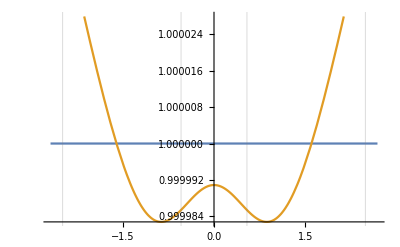

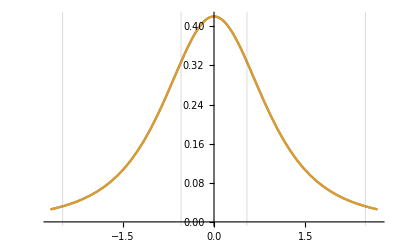

```mathematica
vals= {σ->√3,s->√3/2,delt->√3/100}
gridlines= zerosvalues/.vals//N
toPlot= {1,pst[x, s,σ ]/pstdelta2[x,s,σ,delt] }/.vals;
Plot[toPlot,{x,gridlines[[1]]-0.2,gridlines[[4]]+0.2},GridLines->{gridlines }]
toPlot= {pst[x, s,σ ],pstdelta2[x,s,σ,delt] }/.vals ;
Plot[toPlot,{x,gridlines[[1]]-0.2,gridlines[[4]]+0.2},GridLines->{gridlines }]
```

{σ→10 √2,s→4,delt→(√3)/10}

{-12.4775,-2.46781,2.46781,12.4775}

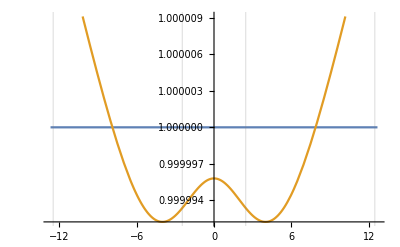

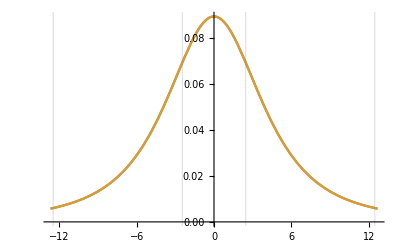

```mathematica
vals= {σ->10 √2,s->4,delt->√3/10}
gridlines= zerosvalues[[1]]/.vals//N
toPlot= {1,pst[x, s,σ ]/pstdelta1[x,s,σ,delt] }/.vals;
Plot[toPlot,{x,gridlines[[1]]-0.2,gridlines[[4]]+0.2},GridLines->{gridlines }]
toPlot= {pst[x, s,σ ],pstdelta1[x,s,σ,delt] }/.vals;
Plot[toPlot,{x,gridlines[[1]]-0.2,gridlines[[4]]+0.2},GridLines->{gridlines }]
```

```mathematica
Solve[(2 σ^2)/(-1+σ^2)==3, σ]
```

{{σ→-√3},{σ→√3}}

```mathematica
(pst[x, s,σ+delt]+1000pst[x, s,σ-delt ])/2
```

1/2 ((2^(-1/2+1/2 (1+(2 σ^2)/(-s^2+σ^2))) (σ^2/((-s^2+σ^2) (x^2/s^2+(2 σ^2)/(-s^2+σ^2))))^(1/2 (1+(2 σ^2)/(-s^2+σ^2))))/(s √(σ^2/(-s^2+σ^2)) Beta[σ^2/(-s^2+σ^2),1/2])+(125 2^(5/2+1/2 (1+(2 σ^2)/(-s^2+σ^2))) (σ^2/((-s^2+σ^2) (x^2/s^2+(2 σ^2)/(-s^2+σ^2))))^(1/2 (1+(2 σ^2)/(-s^2+σ^2))))/(s √(σ^2/(-s^2+σ^2)) Beta[σ^2/(-s^2+σ^2),1/2]))

```mathematica
σ->(s √α)/(√(-2+α))/.α->4/.s->10
```

```mathematica
σ->10 √2
```

σ→10 √2

## Student T Distribuion with scale s and tail exponent α

```mathematica
st[x_, α_, s_]:=((α/(α+ x^2/s^2))^((α+1)/2))/(Sqrt[α]s Beta[α/2,1/2])
```

Let us re-express this expression in terns of its variance:

```mathematica
Integrate[st[x,α,s]1,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]
```

1

```mathematica
Integrate[st[x,α,s]x,{x,-∞, ∞}, Assumptions->{α>2&& s>0}]
```

0

```mathematica
zeros = {x->-(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2),x->-(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),x->(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),x->(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2)} ;
zerovalues = {-(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2),-(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),(s √((5α-√((α+1)(17 α+1))+1)/(α-1)))/(√2),(s √((5α+√((α+1)(17 α+1))+1)/(α-1)))/(√2)}
```

{-(s √((1+5 α+√((1+α) (1+17 α)))/(-1+α)))/(√2),-(s √((1+5 α-√((1+α) (1+17 α)))/(-1+α)))/(√2),(s √((1+5 α-√((1+α) (1+17 α)))/(-1+α)))/(√2),(s √((1+5 α+√((1+α) (1+17 α)))/(-1+α)))/(√2)}

```mathematica
SecondDerivarive = (D[D[(st[x ,α ,s]/.AlphaDefinition), σ], σ]);
SecondDerivarive=SecondDerivarive/.VarianceDefinition[[2]];
```

```mathematica
For[i=1,i<=4,i++,
Print[SecondDerivarive/. zeros[[i]]/.{α->4, s->10} //N] ]
```

{-0.0000539816}

{0.0000956958}

{0.0000956958}

{-0.0000539816}

```mathematica
For[i=1,i<=4,i++,
Print[SecondDerivarive/. zeros[[i]]/.{α->3, s->2.5} //N] ]
```

{-0.00100278}

{0.00249516}

{0.00249516}

{-0.00100278}

```mathematica
stdelta2[x_,α_,s_ ,delt_]=(st[x, α,s √(1+delt)]+st[x, α,s √(1-delt) ])/2 ;
stdelta1[x_,α_,s_ ,delt_]=(st[x, α,s+delt]+st[x, α,s-delt ])/2 ;
```

```mathematica
zerovalues
```

{-(s √((1+5 α+√((1+α) (1+17 α)))/(-1+α)))/(√2),-(s √((1+5 α-√((1+α) (1+17 α)))/(-1+α)))/(√2),(s √((1+5 α-√((1+α) (1+17 α)))/(-1+α)))/(√2),(s √((1+5 α+√((1+α) (1+17 α)))/(-1+α)))/(√2)}

{α→400,s→1000,delt→0.1}

{-2139.39,-661.865,661.865,2139.39}

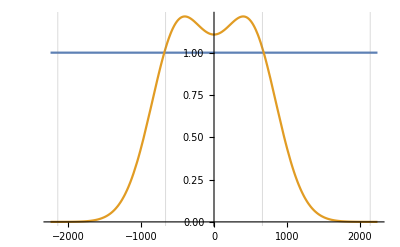

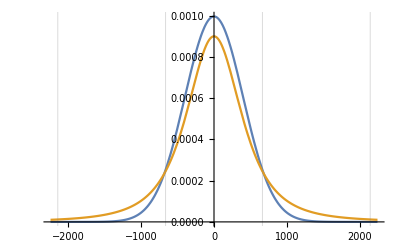

```mathematica
vals= {α->400,s->1000,delt->0.1}
gridlines= zerovalues/.vals//N
toPlot= {1,pst[x, α,s]/pstdelta1[x,α,s,delt] }/.vals;
Plot[toPlot,{x,gridlines[[1]]-100,gridlines[[4]]+100},GridLines->{gridlines }]
toPlot= {pst[x, α,s],pstdelta1[x,α,s,delt] }/.vals ;
Plot[toPlot,{x,gridlines[[1]]-100,gridlines[[4]]+100},PlotLegends->"Expressions",GridLines->{gridlines }]
```

Unlike the gaussian case. In this case the scale perturbed distribution has a lower peak than the unperturbed one and, in addition, the shoulders and tail get fatter !!!!